```mathematica
SetDirectory[NotebookDirectory[]];
Needs["SSS`"];
```

### Code

```mathematica
LeastUsedRulePositions[sss_Association /; KeyExistsQ[sss,"RulesUsed"]] := Module[{ru=sss["RulesUsed"],len,ruletally,least},
len=Length[ru];
ruletally=Tally[ru⟦Round[.1len];;len⟧];      (* skip 10% -- ARBITRARY! -- of rules used, tally the rest *)
least=First@First@SortBy[ruletally,Last];  (* identify the least used rule *)
MergeIntervalsByRulesUsed[Flatten@Position[ru,least],ru]  (* find its occurrences anywhere, merge intervals -- IS THIS NECESSARY?! -- and return *) 
];
```

```mathematica
LeastUsedRulePositions::usage = "Takes sss, an already generated sessie object, and returns the list of positions where the least-used rule was applied (least-used in the last 90% of the evolution).  This list is modified by the function MergeIntervalsByRulesUsed before being returned.";
```

```mathematica
MaxStateLengthPositions[sss_Association /; KeyExistsQ[sss,"Evolution"]]:=Module[{currmaxlenstringlen,strlens,strt,evollen,evol=sss["Evolution"],b=Boole[sss["Verdict"]==="Repeating"]},
evollen=Length[evol];
strlens=StringLength /@ evol;
currmaxlenstringlen=Min[strlens];
strt=First@First[Position[strlens,currmaxlenstringlen,1]];
Most@
MergeIntervalsByRulesUsed[
Last@Last@Reap[
Do[
If[StringLength[evol⟦n⟧]>currmaxlenstringlen-b,(* if repeating, "≥" *)
Sow[n]; currmaxlenstringlen=StringLength[evol⟦n⟧]
],
{n,strt,evollen}]
],
sss["RulesUsed"]
]
];
```

```mathematica
MaxStateLengthPositions::usage = "Takes sss, an already generated sessie object, and returns the list of positions where the sessie state string reached a new maximum length, starting with the minimum length string -- which hopefully eliminates some initial non-pattern stuff.  This list is modified by the function MergeIntervalsByRulesUsed before being returned.";
```

```mathematica
MergeIntervalsByRulesUsed[l0_List,ru_List] := Module[{l=l0,n=Length[l0],rulesused1,rulesused2},
(* Expects a list of interesting integers (l0, defining intervals) and the "RulesUsed" list of some SSS.  Merges any intervals in which fewer different rules were used than in neighboring intervals.
Returns the resulting list, which should be more meaningful than the original one. Give up if length ≤ 2 *) 
While[n>2,
rulesused1=Union[ru⟦l⟦n-2⟧;;l⟦n-1⟧-1⟧];
rulesused2=Union[ru⟦l⟦n-1⟧;;l⟦n⟧-1⟧];
(* If[$debug,Print["rules used:", rulesused1,", ",rulesused2]]; *)
Which[
rulesused1==rulesused2, n--,
SubsetQ[rulesused1,rulesused2], l=Drop[l,{n}];n=Length[l],
SubsetQ[rulesused2,rulesused1], l=Drop[l,{n-2}];n=Length[l],
True,l=Drop[l,{n-1}];n=Length[l]
]
];
l]
```

```mathematica
Clear[ReliableDistances];ReliableDistances[sss_Association /; KeyExistsQ[sss,"OutDegreeRemaining"]] := Module[{len,net=sss["Net"],odr,z,eins,pos,distances,maxdistance},
If[Length[net]==0,Return[{}]];  (* no network, no distances! *)
eins=Min[Flatten[net/.Rule->List]];
If[$debug,Print["smallest node in net: ",eins]];
(* Find the end of last case of the longest run of 0s (or least entry) in the list of remaining outdegrees, after skipping first 10% *)
len=Length[sss["OutDegreeRemaining"]];
odr=ReplacePart[sss["OutDegreeRemaining"],_?(#<.1len&)->∞];  (* set first 10% = ∞, these will be ignored *)
If[$debug,Print["OutDegreeRemaining (massaged): ", odr]];
z = Min[odr];  
If[$debug,Print["treating as zero (in odr): ", z]];
(* for our purposes, z will be treated as 0, nodes that are as complete as possible have outdegree remaining = z *)
If[$debug,Print["using \"OutDegreeRemaining\" to find end of reliable data: ",
(odr /. {Longest[g___,1],f:Longest[z..,2],h___}:>{{g},{f},{h}})]];
pos=(odr /. {Longest[g___,1],f:Longest[z..,2],h___}:>Length[{g,f}]+Flatten@Position[{h},_?(#≠0&)]);If[$debug,Print["Position of first untrustworthy node: ", pos]]; 
(* distances = sss["Distance"]; *)   (* now using undirected graph distances... *)
distances = GraphDistance[UndirectedGraph[sss["Net"]],eins];
If[$debug,Print["distances (uncut): ",distances]];
maxdistance=Min[distances⟦pos⟧];
If[$debug,Print["last distance we'll trust: ", maxdistance]];
distances /. _?(#>maxdistance&)->-1  (* replace unreliable distances by -1 *)
];
```

```mathematica
DistanceLastPositions[sss_Association /; KeyExistsQ[sss,"OutDegreeRemaining"]] := 
(* find the position of the last node with (reliable) distance 1, 2, ... *)
Module[{rd=ReliableDistances[sss]},
If[Length[rd]==0,{},
MergeIntervalsByRulesUsed[
Last[Last[Position[rd,#,{1}]]]& /@ Range[Max[Complement[rd,{∞}]]],
sss["RulesUsed"]
]
]
];
DistanceLastPositions::usage = "Takes sss, an already generated sessie object, and returns the list of positions {n_1, n_2, …, n_k} in its causal network, each of which is the last node at the indicated distance from the origin.  Thus n_1 is the node of maximum index which is 1 step away, n_2 the largest that is 2 steps away, etc. But only the final 90% of the network is considered. This list is modified by the function MergeIntervalsByRulesUsed before being returned.";
```

```mathematica
DistanceTally[sss_Association /; KeyExistsQ[sss,"OutDegreeRemaining"]] :=   
(* tally reliable distances, sort, drop the unreliable (-1 & ∞) tally, keep numbers only *) 
Module[{rd=ReliableDistances[sss]},
If[Length[rd]==0,{},
Accumulate[Last /@ Rest@Sort@DeleteCases[Tally[rd],{∞,_}]]
]
];
DistanceTally::usage = "Takes sss, an already generated sessie object, and returns the list of how many nodes are 0 steps from the origin, how many 1 step away, how many 2 steps away, …. But only the final 90% of the network is considered.";
```

```mathematica
LongestPositiveSubsequence[l_List] := Module[{mx,spl},
spl=SplitBy[l/.ComplexInfinity->∞,0≤#<∞&];
mx=Max[Length/@spl];
First[Select[spl,Length[#]==mx&]]
]
```

```mathematica
Clear[RecognizeDifferenceRow];
RecognizeDifferenceRow[l_List] := Module[{len=Length[l],ptrn,dlay,mtch,mtchlen,k,rats},
For[k=1,k≤len/2,k++,  (* for each possible size moving average run k *)
ptrn=MovingAverage[l,k];
(* Print["ptrn: ",ptrn]; *)
If[MatchQ[ptrn,{Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 5 repeated items between *)
{dlay,mtchlen,mtch}=(ptrn/.{a:Repeated[_,{0,5}],brun:Longest[Repeated[b_,{5,∞}]],Repeated[_,{0,3}]}:>{Length[{a}],Length[{brun}],b}); 
Return[{"dim",{k,dlay,mtchlen,mtch}}]  (* constant row found, needed k-averaging, after dlay, including a mtch of length mtchlen *)
];
Off[Divide::infy,Divide::indet];
rats=LongestPositiveSubsequence[Ratios[ptrn]];  (* try ratios instead *)
(* Print["rats: ",rats]; *)
If[MatchQ[rats,{Repeated[_,{0,5}],Repeated[b_?(#>1&),{3,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 3 repeated positive ratios between *)
{dlay,mtchlen,mtch}=(rats/.{a:Repeated[_,{0,5}],brun:Longest[Repeated[b_?(#>1&),{3,∞}]],Repeated[_,{0,3}]}:>{Length[{a}],Length[{brun}],b});
On[Divide::infy,Divide::indet];
Return[{"exp",{k,dlay,mtchlen,mtch}}] (* exponential, needed k-averaging, after dlay, including a mtch of length mtchlen *)
]
];
{}]  (* {} = failure, {"dim"|"exp", {k, dlay, (max) match length,(diff|ratio)mtch}} = success! *)
```

```mathematica
CheckDimension[l_List]:=Module[{diffsTable={l,Differences[l]},lastrow,ans,k,dlay,mtchlen,mtch},
While[Length[lastrow=Last[diffsTable]]≥5, (* stop when rows become too short *)
ans=RecognizeDifferenceRow[lastrow];  (* try to ID this row *)
If[Length[ans]>0, 
(* success, get details: k-averaging, after dlay, match of length mtchlen *)
{k,dlay,mtchlen,mtch}=ans⟦2⟧;
Return[{
Switch[ans⟦1⟧,
"exp","exp" (* <>ToString[Length[diffsTable]-1] *),
"dim",ToString[Length[diffsTable]-1]<>"D"
],
ans⟦2⟧,
Framed@Grid[diffsTable⟦All,dlay+1;;dlay+k⟧],Grid[diffsTable]}],
(* failure, add another row, try again *)
AppendTo[diffsTable,Differences[Last[diffsTable]]]
]
];
{"failed",Grid[diffsTable]}]
```

```mathematica
Clear[GuessDimension];
SetAttributes[GuessDimension,HoldFirst];
GuessDimension[sss0_] := Module[{len,sss,ans,anssum,vdct,chngd=False,RC},
(* may change the "Verdict" field of the SSS object passed as an argument *)
sss=Evaluate[sss0]; (* local copy to use *)
If[!KeyExistsQ[sss,"Evolution"],Return["Invalid input"]];
If[MatchQ[vdct=sss["Verdict"],"Repeating"|"Dead"], Return[vdct]];  (* already have Repeating or Dead Verdict *)

len=Length[sss["RulesUsed"]];
If[$debug,Print["evol len: ", len]];
ans=DeleteCases[
CheckDimension /@ {MaxStateLengthPositions[sss],LeastUsedRulePositions[sss],DistanceLastPositions[sss],DistanceTally[sss]},
{"failed",___}];
(* extract dim & mtchlen, then sort in decreasing order by matchlen *)
anssum=ReverseSortBy[{#⟦1⟧,#⟦2,3⟧}& /@ ans,Last];  
(* gather by dim, total all matchlens *)
anssum={#⟦1,1⟧,Total[Last/@#]}& /@ GatherBy[anssum,First];
If[$debug,Print[anssum]];

While[len<5000 && anssum⟦1,-1⟧<10+5*Length[anssum],(* try for agreement *)
chngd=True;
sss=SSSEvolve[sss,len*Round[(10+5*Length[anssum]-anssum⟦1,-1⟧)/5]];  (* extend the sss evolution a bit, depending *)
len=Length[sss["RulesUsed"]];
If[$debug,Print["evol len: ", len]];
ans=DeleteCases[
CheckDimension /@ {MaxStateLengthPositions[sss],LeastUsedRulePositions[sss],DistanceLastPositions[sss],DistanceTally[sss]},
{"failed",___}];
(* extract dim & mtchlen, then sort in decreasing order by matchlen *)
anssum=ReverseSortBy[{#⟦1⟧,#⟦2,3⟧}& /@ ans,Last];  
(* gather by dim, total all matchlens *)
anssum={#⟦1,1⟧,Total[Last/@#]}& /@ GatherBy[anssum,First];
If[$debug,Print[anssum]];
];
vdct=If[Length[anssum]==1,anssum⟦1,1⟧ (* agree! *), anssum (* disagree *)];  
If[len<5000 , chngd=True; sss["Verdict"]=vdct]; (* trust it *)
If[chngd,sss0=sss]; (* update it if changed *)
Print[vdct];
ans
];
```

```mathematica
ToNetDifferenceSets::usage ="ToNetDifferenceSets[net] takes a network given as a list of rules and returns a list of difference sets (sets of link lengths for each node) describing the same network.  A set {n1, n2, ...} in position i lists the indicates that net contained edges {i->n1, i->n2, ...}.";
FromNetDifferenceSets::usage ="FromNetDifferenceSets[l] takes a list l of sets of link lengths for each node of a network and returns the network described.  A set {n1, n2, ...} in position i of l corresponds to {i->n1, i->n2, ...} in the network.";
ToReducedNetDifferenceSets::usage ="ToNetDifferenceSets[l] takes a list l of sets of link lengths for each node of a network and returns a reduced version in which duplicates or duplicate subsequences are summarized using the format n·{…}.";
```

```mathematica
ToNetDifferenceSets[net:{__Rule}] :=Module[{nodediffpairs},
nodediffpairs =  {#⟦1⟧,#⟦2⟧-#⟦1⟧}& /@ net;
Rest /@ 
Map[Last, 
Gather[Join[{#,0}& /@Range[Max[First/@nodediffpairs]],nodediffpairs],First[#1]==First[#2]&],
{2}]
];
```

```mathematica
FromNetDifferenceSets[diffs:{__List}] := Flatten[MapIndexed[Rule[First[#2],First[#2]+#1]&,diffs,{2}]];
```

```mathematica
ToReducedNetDifferenceSets[l_List]:=SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
(*
,
{x:PatternSequence[a:{___Integer}]}:>CenterDot[1,{a}]
*)
}];
(* 1st line looks for a repeated set (2 to ∞ reps) of (0 or more) integers, 2nd line looks for a repeated subsequence (2 to ∞ reps) of at least 2 sets of integers,
3rd line applies to all left over sets. *)

FromReducedNetDifferenceSets[ll_List]:=Flatten[ll /.(n_)·l_List :>Sequence@@Table[l,{n}],1]
```

```mathematica
ToNetDifferenceSets[net:{__Rule}] :=Module[{nodediffpairs, paddedlist,gatheredlist,lasteltslist},
nodediffpairs =  {#⟦1⟧,#⟦2⟧-#⟦1⟧}& /@ net;  (* this creates a pair of integers from each link in the network:  {starting node, link length} *)
paddedlist = Join[{#,0}& /@ Range[Max[First/@nodediffpairs]],nodediffpairs];
gatheredlist=Gather[paddedlist,First[#1]==First[#2]&];
lasteltslist=Map[Last, gatheredlist,{2}];
If[$debug, 
Print["net: ", net]; 
Print["list of {node, link_length} pairs: ", nodediffpairs];
Print["after padding (in case some nodes don't start links): ", paddedlist];
Print["after gathering: ", gatheredlist];
Print["taking only last elements at the 2nd level: ", lasteltslist];
Print["the result now is obtaining by dropping all padded 0s"]
];
Rest /@  lasteltslist
];
```

```mathematica
FromNetDifferenceSets[diffs:{__List}] := (
If[$debug,
Print["netdiffs: ",diffs];
Print["output of MapIndexed: ",MapIndexed[##&,diffs,{2}]];
Print["keeping only 1st index coordinate: ",MapIndexed[{#1,First[#2]}&,diffs,{2}]];
Print["reversing order: ",MapIndexed[{First[#2],#1}&,diffs,{2}]];
Print["building the links: ",MapIndexed[Rule[First[#2],First[#2]+#1]&,diffs,{2}]];
Print["then flatten the result: "];
];
Flatten@MapIndexed[Rule[First[#2],First[#2]+#1]&,diffs,{2}]
)
```

```mathematica
Clear[SetSubtract];
SetSubtract[s2:{___Integer},s1:{___Integer}] := Module[{len1,len2},
If[(len1=Length[s1])<(len2=Length[s2]),∞,Join[s2-s1⟦1;;len2⟧,Table[∞,len1-len2]]]];
SetSubtract[(n2_Integer)·(s2:{{___Integer}..}),(n1_Integer)·(s1:{{___Integer}..})] := Module[{len1,len2},
Which[
n1>n2,∞,
(len1=Length[s1])<(len2=Length[s2]),∞,
True,(n2-n1)·Join[SetSubtract[s2,s1⟦1;;len2⟧],Table[∞,len1-len2]]
]];
SetSubtract[l2_List,l1_List] := 
If[Length[l1]==Length[l2],MapThread[SetSubtract,{l2,l1}]];
SetSubtract::usage="SetSubtract[s1,s2] or SetSubtract[n1·s1,n2·s2] performs a strange sort of 'set subtraction', in which elements of s2 are subtracted in order from the corresponding elements of s1, if the set sizes are the same, so SetSubtract[{1,4,9},{1,2,3}] gives {0,2,6}.  If s1 is longer than s2, the value ∞ is returned, if s2 is longer than s1, elements are subtracted until they run out, and the remaining subtractions return ∞. If n1>n2, the difference is given in the response, otherwise the entire expression returns ∞.";
```

```mathematica
idMatch[{x___,(reps_Integer)·(match_List),z___}] := {Length[{x}],reps,match,Length[{z}]};
```

```mathematica
RecognizeNetDifferences[l_List] := Module[{tbl,offst,cnt,ptrn,ttl,dlay,repcnt,mtch,xcs},
(* table of set differences for all offsets *)
tbl=Table[SetSubtract[l[[k;;]],l[[;;-k]]],{k,2,Length[l]/2}];
Print[Grid[tbl]];
(* find count, offset and matched pattern for the best one = most 0s *)
{cnt,offst,ptrn}=First@MaximalBy[MapIndexed[{Count[#1,_?NonNegative,∞],First@#2,#1}&,tbl,1],First];
ttl=Count[ptrn,_?AtomQ,∞]; (* maximum number of 0s possible *)
Print["{count, offset, pattern, total}: ",{cnt,offst,ptrn,ttl}];

If[cnt/ttl≥0.9 , (* covers 90% of the cases *)

{dlay,repcnt,mtch,xcs}=idMatch@SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
}] ;

Print[{dlay,repcnt,mtch,xcs}];
Return[{ToString[100.*cnt/ttl]<>"%",{offst,dlay,repcnt,mtch,xcs}}]  (* after dlay *)
]];
```

```mathematica
RecognizeNetSetDifferenceRow[l:((_List)..)] := Module[{len=Length[l],ptrn,dlay,mtch,k},

For[k=1,k≤len/2,k++,  (* for each possible offset size k *)
ptrn=MovingAverage[l,k];
If[MatchQ[ptrn,{Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 5 repeated items between *)
{dlay,mtch}=(ptrn/.{a:Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}:>{Length[{a}],b}); 
Return[{"dim",{k,dlay,mtch}}]  (* dimension k, after dlay *)
];
];
{}]  (* {} = failure, {"dim", {k,dlay,(diff|ratio)mtch}} = success! *)
```

```mathematica
Clear[NetSummary];

Format[NetSummary[x__, {var_, start_, finish_}]] :=
  DisplayForm[
   RowBox[{UnderoverscriptBox["𝕊", RowBox[{var, "=", start}], finish],
     "[", Sequence @@ Riffle[{x}, ","], "]"}]];

NetSummary /: Expand[NetSummary[x__, {var_, start_Integer, finish_Integer}]] :=
 Join @@ Table[{x}, {var, start, finish}];

NetSummary /: ExpandAll[NetSummary[x__, {var_, start_Integer, finish_Integer}]] :=
 Join @@ Table[{x}/.NetSummary[y___]:>Sequence@@(ExpandAll[NetSummary[y]]), {var, start, finish}]
```

```mathematica
NetSummarize[l:{((_·{___})|{___})..}] :=Module[{lpat,chunksize=1,lpatpart,lpatpartpairs,booletable={},goodness,maxrunlens,fracs,pos,goodchunks,intpos,ans,tail,theoreticaltail,i,j,n,term,fnlans},
lpat = (l /. _Integer->"i"); (* replace all integers by "i" *)
For[chunksize=1,chunksize<=Length[lpat]/4,chunksize++,  (* loop on viable chunksize *)
lpatpart=Partition[lpat,chunksize];
lpatpartpairs=Partition[lpatpart,2,1]; (* we will compare neighbors *)
AppendTo[booletable,Boole[SameQ @@@ lpatpartpairs]]  (* 1 = match, 0 = no match *)
];
Print@Grid@booletable;
goodness=Split/@booletable;    (* split each line into runs *)
(* Print[goodness]; *)
goodness=ReplaceAll[goodness,{x:{1..}:>Length[x],{0..}->0}];  (* count the runs of 1s, replace runs of 0s by a single 0 *)
(* Print[goodness]; *)
maxrunlens=Max /@ goodness;  (* find longest run of 1s in each row *)
Print[1+maxrunlens];  (* greatest number of matching chunks in each row *)
fracs=(If[#<2,0,#+1]&/@maxrunlens)^2/(1+Length/@ booletable);
(* Initial triage here, if <2 comparisons, i.e., if <3 matching chunks, replace by 0.  Max number of matches compared to possible number.  Later, after forward/backward extension, also count items in the original list and consider what fraction of the unreduced NetDifferenceSets list is explained. *)
Print[fracs];
chunksize=First@First@Position[fracs,Max[fracs]];
Print["best row / best chunk size: ",chunksize];
If[fracs[[chunksize]]<1,
Print["Unable to fit"];Print@Grid@booletable;Print[chunksize,": ",maxrunlens+1, ": ",fracs];
Return[]
];
pos={0,1}+First@SequencePosition[booletable[[chunksize]],{Repeated[1,{maxrunlens[[chunksize]]}]}];
Print[pos];
goodchunks=Partition[l,chunksize][[Span@@pos]]; (* these are the chunks to use *)
Print@Column[goodchunks];
intpos=GatherBy[Position[goodchunks,_Integer],Rest]; (* find & sort positions of integers *)
(* Print[intpos]; *)
(* Print[Extract[goodchunks,#]& /@ intpos]; *)
(* Print[FindSequenceFunction[Extract[goodchunks,#],n]& /@ intpos]; *)
(* Print[Thread[(First/@intpos)->(FindSequenceFunction[Extract[goodchunks,#],n]& /@ intpos)]]; *)
ans=First @ ReplacePart[goodchunks,Thread[(First/@intpos)->(FindSequenceFunction[Extract[goodchunks,#],ToExpression["n"]]& /@ intpos)]];

Print["ans: ",ans];
Print[NetSummary[Sequence@@ans,{ToExpression["n"],1,pos[[2]]-pos[[1]]+1}]];
Print[Expand@NetSummary[Sequence@@ans,{ToExpression["n"],1,pos[[2]]-pos[[1]]+1}]];
(* check validity of what we found *)
If[Flatten[goodchunks,1]!=Expand@NetSummary[Sequence@@ans,{ToExpression["n"],1,pos[[2]]-pos[[1]]+1}],
Print["Chunksize: ",chunksize];
Print@Flatten[goodchunks,1];
Print@Expand@NetSummary[Sequence@@ans,{ToExpression["n"],1,pos[[2]]-pos[[1]]+1}];
Print["Supposed match pattern: ",ans];
Return[]
];
Print["Checks out correctly for identified section"];
Print@NetSummary[Sequence@@ans,{ToExpression["n"],1,pos[[2]]-pos[[1]]+1}];

tail=l[[pos[[2]]*chunksize+1;;]];
If[Length[tail]>0,
theoreticaltail=Take[
Expand@NetSummary[Sequence@@ans,{ToExpression["n"],pos[[2]]-pos[[1]]+2,
pos[[2]]-pos[[1]]+2+(Ceiling[Length[l]/chunksize]-pos[[2]])}],
Length[tail]];
tailmatch=MapThread[Boole[SameQ[#1,#2]]&,{theoreticaltail,tail}]+
MapThread[Boole[SubsetQ[#1,#2]]&,{theoreticaltail,tail}];

Print["Length[tail] = ",Length[tail], " : ",tailmatch]
];

(* now try to extend backwards *)
i=(pos[[1]]-1)*chunksize; j=0;
(* just to the left of checked section in l, left (wrapping around) in pattern *)
While[i>0,
term=(ans[[Mod[j,chunksize,1]]] /. ToExpression["n"]->2-pos[[1]]+Quotient[i,chunksize,1]);
If[MatchQ[term,{___Integer}],
If[!(And@@(Positive/@term)),Break[]]; (* invalid prediction, quit loop *)
If[l[[i]]!=term,Break[]]  (* non-match, quit loop *)
];
If[MatchQ[term,(n_Integer /; n<0)·(_List)], Break[]];
If[MatchQ[term,0·(_List)],j--;Continue[]]; (* missing term ok *)
If[MatchQ[term,(_Integer)·{___List}] &&
 !(And@@(Positive/@Flatten[List@@term])), Break[]]; (* not all positive *)
If[l[[i]]!=term,Break[]];  (* non-match, quit *)
i--; j--];  (* back up until no match or i==0 (past beginning of list) *)
i++;j++;        (* step back to last actual match *)

Print["{i,j}=",{i,j}];
If[i==1,
Print["Match from beginning"],
Print["Initial non-matching terms: ",l[[;;i-1]]]
];

fnlans=ans;
Do[
fnlans=Prepend[Most[fnlans],(Last@fnlans)/. ToExpression["n"]->ToExpression["n-1"]],
1-j (* if j=0, do once, for j<0, repeat ... *)];


NetSummary[Sequence@@fnlans,{ToExpression["n"],1,Ceiling[(Length[l]-i+1)/chunksize]}]

];
NetSummarize[lm]
```

NetSummarize[lm]

## Some random reverse engineering attempts

```mathematica
NetSummary[n·{{n,n+1}},{n,1,∞}]
```

𝕊_(n=1)^∞[n·{{n,n+1}}]

```mathematica
ExpandAll[NetSummary[n·{{n,n+1}},{n,1,15}]]
```

{1·{{1,2}},2·{{2,3}},3·{{3,4}},4·{{4,5}},5·{{5,6}},6·{{6,7}},7·{{7,8}},8·{{8,9}},9·{{9,10}},10·{{10,11}},11·{{11,12}},12·{{12,13}},13·{{13,14}},14·{{14,15}},15·{{15,16}}}

```mathematica
FromReducedNetDifferenceSets[%]//Short
```

{{1,2},{2,3},{2,3},{3,4},«112»,{15,16},{15,16},{15,16},{15,16}}

```mathematica
FromNetDifferenceSets[%]//Short
```

{1→2,1→3,2→4,2→5,3→5,«230»,118→134,119→134,119→135,120→135,120→136}

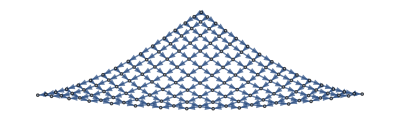

```mathematica
Graph[%,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
NetSummary[(n+1)·{{n,n+1}},{n,1,∞}]
ExpandAll[NetSummary[(n+1)·{{n,n+1}},{n,1,20}]]
Graph3D@FromNetDifferenceSets@FromReducedNetDifferenceSets@%
```

𝕊_(n=1)^∞[(n+1)·{{n,n+1}}]

{2·{{1,2}},3·{{2,3}},4·{{3,4}},5·{{4,5}},6·{{5,6}},7·{{6,7}},8·{{7,8}},9·{{8,9}},10·{{9,10}},11·{{10,11}},12·{{11,12}},13·{{12,13}},14·{{13,14}},15·{{14,15}},16·{{15,16}},17·{{16,17}},18·{{17,18}},19·{{18,19}},20·{{19,20}},21·{{20,21}}}

-Graphics3D-

```mathematica
NetSummary[n·{{n,n+1,n+2}},{n,1,5}]
ExpandAll[NetSummary[n·{{n,n+1,n+2}},{n,1,10}]]
Graph3D@FromNetDifferenceSets@FromReducedNetDifferenceSets@%
```

𝕊_(n=1)^5[n·{{n,1+n,2+n}}]

{1·{{1,2,3}},2·{{2,3,4}},3·{{3,4,5}},4·{{4,5,6}},5·{{5,6,7}},6·{{6,7,8}},7·{{7,8,9}},8·{{8,9,10}},9·{{9,10,11}},10·{{10,11,12}}}

-Graphics3D-

```mathematica
NetSummary[n·{{n,n+2}},{n,1,5}]
ExpandAll[NetSummary[n·{{n,n+2}},{n,1,25}]]
Graph3D@FromNetDifferenceSets@FromReducedNetDifferenceSets@%
```

𝕊_(n=1)^5[n·{{n,2+n}}]

{1·{{1,3}},2·{{2,4}},3·{{3,5}},4·{{4,6}},5·{{5,7}},6·{{6,8}},7·{{7,9}},8·{{8,10}},9·{{9,11}},10·{{10,12}},11·{{11,13}},12·{{12,14}},13·{{13,15}},14·{{14,16}},15·{{15,17}},16·{{16,18}},17·{{17,19}},18·{{18,20}},19·{{19,21}},20·{{20,22}},21·{{21,23}},22·{{22,24}},23·{{23,25}},24·{{24,26}},25·{{25,27}}}

-Graphics3D-

𝕊_(n=1)^5[2·{{n,n+1}}]

{2·{{1,2}},2·{{2,3}},2·{{3,4}},2·{{4,5}},2·{{5,6}},2·{{6,7}},2·{{7,8}},2·{{8,9}},2·{{9,10}},2·{{10,11}},2·{{11,12}},2·{{12,13}},2·{{13,14}},2·{{14,15}},2·{{15,16}},2·{{16,17}},2·{{17,18}},2·{{18,19}},2·{{19,20}},2·{{20,21}},2·{{21,22}},2·{{22,23}},2·{{23,24}},2·{{24,25}},2·{{25,26}},2·{{26,27}},2·{{27,28}},2·{{28,29}},2·{{29,30}},2·{{30,31}},2·{{31,32}},2·{{32,33}},2·{{33,34}},2·{{34,35}},2·{{35,36}},2·{{36,37}},2·{{37,38}},2·{{38,39}},2·{{39,40}},2·{{40,41}},2·{{41,42}},2·{{42,43}},2·{{43,44}},2·{{44,45}},2·{{45,46}},2·{{46,47}},2·{{47,48}},2·{{48,49}},2·{{49,50}},2·{{50,51}}}

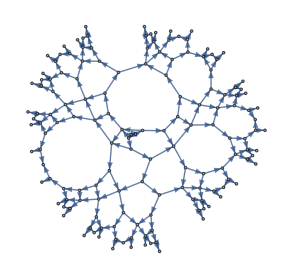

```mathematica
NetSummary[2·{{n,n+1}},{n,1,5}]
ExpandAll[NetSummary[2·{{n,n+1}},{n,1,50}]]
Graph@FromNetDifferenceSets@FromReducedNetDifferenceSets@%
```

```mathematica
NetSummary[3·{{n,n+1}},{n,2,5}]
ExpandAll[NetSummary[3·{{n,n+1}},{n,2,50}]]
Graph3D@FromNetDifferenceSets@FromReducedNetDifferenceSets@%
```

𝕊_(n=2)^5[3·{{n,n+1}}]

{3·{{2,3}},3·{{3,4}},3·{{4,5}},3·{{5,6}},3·{{6,7}},3·{{7,8}},3·{{8,9}},3·{{9,10}},3·{{10,11}},3·{{11,12}},3·{{12,13}},3·{{13,14}},3·{{14,15}},3·{{15,16}},3·{{16,17}},3·{{17,18}},3·{{18,19}},3·{{19,20}},3·{{20,21}},3·{{21,22}},3·{{22,23}},3·{{23,24}},3·{{24,25}},3·{{25,26}},3·{{26,27}},3·{{27,28}},3·{{28,29}},3·{{29,30}},3·{{30,31}},3·{{31,32}},3·{{32,33}},3·{{33,34}},3·{{34,35}},3·{{35,36}},3·{{36,37}},3·{{37,38}},3·{{38,39}},3·{{39,40}},3·{{40,41}},3·{{41,42}},3·{{42,43}},3·{{43,44}},3·{{44,45}},3·{{45,46}},3·{{46,47}},3·{{47,48}},3·{{48,49}},3·{{49,50}},3·{{50,51}}}

-Graphics3D-

```mathematica
NetSummary[n^2·{{n,n+1}},{n,1,∞}]
ExpandAll[NetSummary[n^2·{{n,n+1}},{n,1,10}]]
Graph3D@FromNetDifferenceSets@FromReducedNetDifferenceSets@%
```

𝕊_(n=1)^∞[n^2·{{n,1+n}}]

{1·{{1,2}},4·{{2,3}},9·{{3,4}},16·{{4,5}},25·{{5,6}},36·{{6,7}},49·{{7,8}},64·{{8,9}},81·{{9,10}},100·{{10,11}}}

-Graphics3D-

```mathematica
NetSummary[(n-1)·{{n,n+1}},{n,1,∞}]
ExpandAll[NetSummary[(n-1)·{{n,n+1}},{n,1,50}]]
Graph3D@FromNetDifferenceSets@FromReducedNetDifferenceSets@%
```

𝕊_(n=1)^∞[(n-1)·{{n,n+1}}]

{0·{{1,2}},1·{{2,3}},2·{{3,4}},3·{{4,5}},4·{{5,6}},5·{{6,7}},6·{{7,8}},7·{{8,9}},8·{{9,10}},9·{{10,11}},10·{{11,12}},11·{{12,13}},12·{{13,14}},13·{{14,15}},14·{{15,16}},15·{{16,17}},16·{{17,18}},17·{{18,19}},18·{{19,20}},19·{{20,21}},20·{{21,22}},21·{{22,23}},22·{{23,24}},23·{{24,25}},24·{{25,26}},25·{{26,27}},26·{{27,28}},27·{{28,29}},28·{{29,30}},29·{{30,31}},30·{{31,32}},31·{{32,33}},32·{{33,34}},33·{{34,35}},34·{{35,36}},35·{{36,37}},36·{{37,38}},37·{{38,39}},38·{{39,40}},39·{{40,41}},40·{{41,42}},41·{{42,43}},42·{{43,44}},43·{{44,45}},44·{{45,46}},45·{{46,47}},46·{{47,48}},47·{{48,49}},48·{{49,50}},49·{{50,51}}}

-Graphics3D-

𝕊_(n=1)^∞[n·{{n}}]

{1·{{1}},2·{{2}},3·{{3}},4·{{4}},5·{{5}},6·{{6}},7·{{7}},8·{{8}},9·{{9}},10·{{10}}}

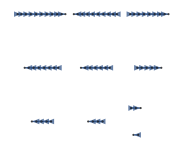

```mathematica
NetSummary[n·{{n}},{n,1,∞}]
ExpandAll[NetSummary[n·{{n}},{n,1,10}]]
Graph[FromNetDifferenceSets@FromReducedNetDifferenceSets@%,GraphLayout->{PackingLayout->"NestedGrid"}]
```

```mathematica
NetSummary[(n-1)·{{n,n+1}},{n,1,∞}]
ExpandAll[NetSummary[(n-1)·{{n,n+1}},{n,1,100}]]//Short
Graph3D[g1=FromNetDifferenceSets@FromReducedNetDifferenceSets@%]
```

𝕊_(n=1)^∞[(n-1)·{{n,n+1}}]

{0·{{1,2}},1·{{2,3}},2·{{3,4}},«95»,98·{{99,100}},99·{{100,101}}}

-Graphics3D-

```mathematica
GraphDistance[g1,1]//Short[#,10]&
```

{0,1,1,∞,∞,2,2,2,2,3,3,3,3,3,3,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,«4847»,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95}

```mathematica
Tally[%]/. {a_,b_}:>b·{a}
```

{1·{0},2·{1},2·{∞},4·{2},6·{3},7·{4},9·{5},10·{6},11·{7},12·{8},13·{9},14·{10},15·{11},17·{12},18·{13},19·{14},20·{15},21·{16},22·{17},23·{18},24·{19},25·{20},26·{21},27·{22},28·{23},29·{24},30·{25},31·{26},33·{27},34·{28},35·{29},36·{30},37·{31},38·{32},39·{33},40·{34},41·{35},42·{36},43·{37},44·{38},45·{39},46·{40},47·{41},48·{42},49·{43},50·{44},51·{45},52·{46},53·{47},54·{48},55·{49},56·{50},57·{51},58·{52},59·{53},60·{54},61·{55},62·{56},63·{57},65·{58},66·{59},67·{60},68·{61},69·{62},70·{63},71·{64},72·{65},73·{66},74·{67},75·{68},76·{69},77·{70},78·{71},79·{72},80·{73},81·{74},82·{75},83·{76},84·{77},85·{78},86·{79},87·{80},88·{81},89·{82},90·{83},91·{84},92·{85},93·{86},94·{87},95·{88},96·{89},97·{90},98·{91},99·{92},100·{93},101·{94},26·{95}}

```mathematica
Subtract[
%261[[6;;-2]] /. n_·{a_}:>{a,n},
%261[[4;;-4]]/. n_·{a_}:>{a,n}] /. {a_,n_}:>n·{a}
```

{3·{2},3·{2},3·{2},2·{2},2·{2},2·{2},2·{2},2·{2},3·{2},3·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},3·{2},3·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},3·{2},3·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2}}

```mathematica
{3·3·{2},5·2·{2},2·3·{2},13·2·{2},2·3·{2},29·2·{2},2·3·{2},(>=36)·2·{2}}
```

```mathematica
NetSummary[n·{{n,n+1,n+2,n+3}},{n,1,5}]
ExpandAll[NetSummary[n·{{n,n+1,n+2,n+3}},{n,1,10}]]
Graph3D@FromNetDifferenceSets@FromReducedNetDifferenceSets@%
```

𝕊_(n=1)^5[n·{{n,n+1,n+2,n+3}}]

{1·{{1,2,3,4}},2·{{2,3,4,5}},3·{{3,4,5,6}},4·{{4,5,6,7}},5·{{5,6,7,8}},6·{{6,7,8,9}},7·{{7,8,9,10}},8·{{8,9,10,11}},9·{{9,10,11,12}},10·{{10,11,12,13}}}

-Graphics3D-